# Določitev števila π z metodo Monte Carlo

```mathematica
Get["C:\\Users\\zupan\\Documents\\Faks\\3. letnik\\1. semester\\NRO\\Domače naloge\\Domača naloga2\\mcc_pi.m"]
```

```mathematica
Nš=100000; (*Poljubno število točk, ki jih bomo uporabili za izračun števila π*)
```

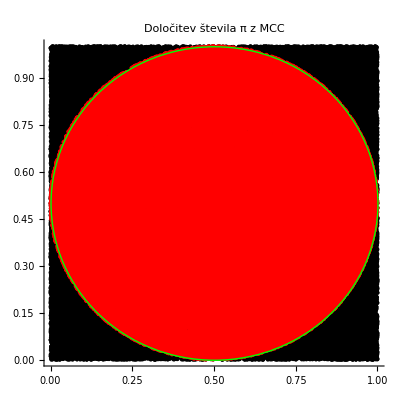

```mathematica
mccpi[Nš];
(*krožnica = RegionMember[Disk[{0.5,0.5}, 0.5]]; definiramo krožnico, s katero bomo računali število π*)

VseTočke=Graphics[Point[točke]];
NotranjeTočke=Graphics[{Red,Point[Pick[točke,krožnica[točke]]]}];
Krožnica=Graphics[{Green, Circle[{0.5,0.5},0.5]}];
Show[VseTočke, NotranjeTočke,Krožnica,
Axes->True,PlotLabel->"Določitev števila π z MCC"
]
```

```mathematica
(*Izračun približka števila π*)
πprib=4.Count[krožnica[točke],True]/Length[točke]
```

3.13916

```mathematica
(*Izračun napake*)
Napaka[πpri_]:=Module[{pi=πpri},Abs[π-pi]]

Napaka[πprib]
```

0.00243265

# Razvoj v vrsto

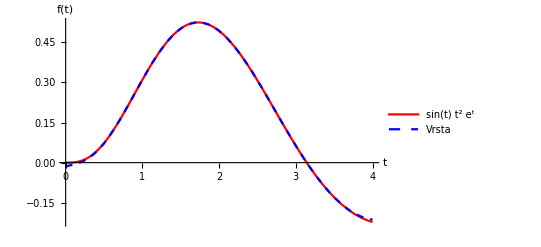

```mathematica
t0=2; (*Točka okoli, katere delamo razvoj*)
n=10; (*Red razvoja*)

graf1=Plot[Sin[x]*x^2*Exp[-x], {x,0,4},PlotStyle->Red,PlotLegends->{"sin(t) t^2 e^t"}];
graf2=Plot[Evaluate[Normal[Series[Sin[x]*x^2*Exp[-x], {x,t0, n}]]], {x,0,4},PlotStyle->{Blue, Dashed},PlotLegends->{"Vrsta"}];
Show[graf1,graf2,AxesLabel->{"t","f(t)"}]
```

```mathematica
Clear[n]
(*Plot, za katerega lahko spreminjamo red razvoja v vrsto od 1 do 10:*)
Manipulate[Plot[Evaluate[Normal[Series[Sin[x]*x^2*Exp[-x], {x,t0, n}]]], {x,0,4},PlotStyle->{Blue, Dashed},AxesLabel->{"t","f(t)"}],{n,1,10,1}]
```